# Mathematica Practice

## Linear Differential Equations

We will try to solve two Non Linear differential equations which need to be solve analytically and examples of the solutions are to be plotted

```mathematica
(*Remove all Global Variables from previous run time*)
Quiet[Remove["Global'*"]]
```

```mathematica
(*
DSolveValue solves differential equastion in Mathematica it is solving for y(t)
y'[t]+y[t]/τ== DiracDelta[t] is the first order system we want to solve where DiracDelta[t] is the 
impulse input that is applied on the low pass filter system.
y[0]==HeavisideTheta[0] is the initial condition at t= 0, 
y[t] expression to evaluate
t is the independent variable
ht is the impulse response function for the system 
*)
ht = DSolveValue[{y'[t]+y[t]/τ== DiracDelta[t],y[0]==HeavisideTheta[0]},y[t],t]//Flatten
(*Diract Delta is a function such that it is zero at everywhere except t=0 at t=0 its value is inifinite in such a way that it integrates to 1 *)
```

ⅇ^(-t/τ) HeavisideTheta[t]

Now make a list

```mathematica
(*This is a list of replacement rules where we replace the symbol τ with 1 *)
values ={τ->1} 
(*Substitues the value of τ in the equation we got after solving ht *)
ht1 = ht/.values
```

{τ→1}

ⅇ^-t HeavisideTheta[t]

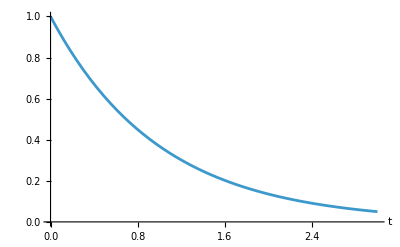

```mathematica
Plot[ht1, {t, 0, 3}, AxesLabel -> Automatic]
```

```mathematica
(*
ht/.{τ->a} substitutes with whatever value a has 
Manipulate[Plot Syntax, {{variable, starting value}, minimum values, maximum value}]
*)
Manipulate[Plot[ht/.{τ->a},{t, 0, tend},AxesLabel->Automatic, PlotRange->{0,1}],{{a,1},0.1,10},{{tend,3},0.1,100}]
```

```mathematica
(*Module in Mathematica is a method equivalent of python.
Format *)
(*Module[{localVar1, localVar2, ...}, expression]*)

modfirst[τ_, tend_] := Module[{ht},
							ht = DSolveValue[{y'[t]+y[t]/τ== DiracDelta[t],y[0]==HeavisideTheta[0]},y[t],t];
							Plot[ht, {t, 0, tend}, AxesLabel -> Automatic,PlotRange->{0,1}]]
```

```mathematica
Manipulate[modfirst[a,tend],{{a,1},0.1,10},{{tend, 3},0.1,100}]
```

## Step Response of 1st Order System

A step response is when the input is changed from 0 to a constant values and the values is kept there, unlike a impulse response where we get a quick spike at t=0 and then nothing .

```mathematica
(*Intuitively a step response is the integral of all the Impulse responses integrated over a time t*)
s1t = Integrate[ht, t]
(*HeavisideTheta is step function which equals 1 is t>= 0 ortherwise 0.*)
```

(τ-ⅇ^(-t/τ) τ) HeavisideTheta[t]

```mathematica
s1t1 = s1t/.values
```

(1-ⅇ^-t) HeavisideTheta[t]

```mathematica
(*Other way to solve this solve the differential equation with the function as HeavisideTheta 
same thing as before just change up the function on the right side of the differential equation*)
s2t = DSolveValue[{y'[t]+y[t]/τ==HeavisideTheta[t],y[0]==0},y[t],t]//Simplify
```

(1-ⅇ^(-t/τ)) τ HeavisideTheta[t]

```mathematica
(*Now we apply the values to s2t and plot it *)
s2t1 = s2t/.values
```

(1-ⅇ^-t) HeavisideTheta[t]

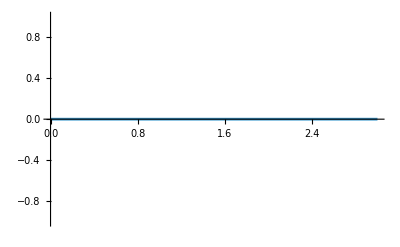

```mathematica
Plot[s2t1-s1t1, {t,0,3}, PlotRange->All]
```

## Non Linear Differential Equations : SIR Model

```mathematica
(*Define the initial values for the system of ODE's*)
values = {s0 -> 1, i0->10^-5, r0->0, tend ->40, γ->1/7, R0->10}
(*Solve the Non Linear Differential Equation using NDSolveValue from t=0 to t=tend*)
{st, it, rt} = NDSolveValue[{s'[t]==-R0*γ*i[t]*s[t],
							i'[t]==R0*γ*i[t]*s[t]-γ*i[t],
							r'[t]== γ*i[t],
							s[0]==s0,
							i[0]==i0,
							r[0]==r0}/.values,{s[t],i[t],r[t]},{t,0, tend/.values}]
```

{s0→1,i0→1/100000,r0→0,tend→40,γ→1/7,R0→10}

{InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t]}

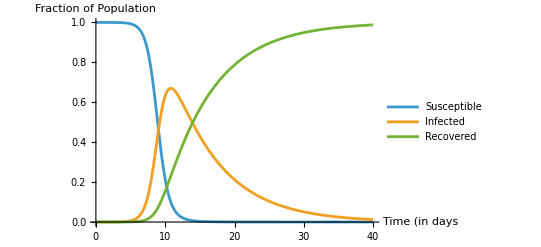

```mathematica
Plot[{st,it, rt}, {t, 0, tend/.values},
PlotLegends->{"Susceptible","Infected","Recovered"},AxesLabel->{"Time (in days", "Fraction of Population"}]
```

```mathematica
(*Compute the final values*)
{stend, itend, rtend} = {st, it, rt}/.{t ->tend/.values}
(*Replaces the t with tend*)
max = FindMaximum[it/.values, {t,10}]
```

{0.0000513188,0.0122203,0.987738}

{0.669752,{t→10.8089}}

```mathematica
(*Writing a function called modSIR and reproduce the plot as given in the exercise*)
modSIR[i0_:1/90, γ_:1/4, R0_:4/3,
	tend_:(7*14), s0_ :1, r0_:0]:=
	Module[{},{st, it, rt}=NDSolveValue[
	{s'[t]==-R0*γ*s[t]*i[t],
i'[t]==R0*γ*s[t]*i[t]-γ*i[t],
r'[t]==γ*i[t],
s[0]==s0,
i[0]==i0,
r[0]==r0},{s[t],i[t],r[t]},{t, 0, tend}];
	Plot[{st, it, rt},{t,0,tend},
	PlotLegends->{"Susceptible", "Infected","Recovered"},AxesLabel ->
{"Time (days)","Fraction of Population"}]]
modSIR[]
```

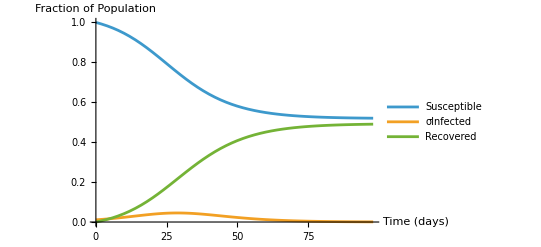

```mathematica
(*Now we use Manipulate to study the modSIR module and control for R0 and tend*)
Manipulate[modSIR[10^-4,1/7,R0,tend],{R0,0,10},{tend,1,1000}]
```

```mathematica
DynamicModule[{R0=1.11,tend=1000.},modSIR[1/10^4,1/7,R0,tend]]
```

```mathematica
DynamicModule[{R0=0.99,tend=1000.},modSIR[1/10^4,1/7,R0,tend]]
```

```mathematica
(*Write a function modSIRend which only returns the value rtend*)
modSIRend[i0_:1/90, γ_:1/4, R0_:4/3,
	tend_:(7*14), s0_ :1, r0_:0]:=
	Module[{},{st, it, rt}=NDSolveValue[
	{s'[t]==-R0*γ*s[t]*i[t],
i'[t]==R0*γ*s[t]*i[t]-γ*i[t],
r'[t]==γ*i[t],
s[0]==s0,
i[0]==i0,
r[0]==r0},{s[t],i[t],r[t]},{t, 0, tend}];
	rtend = rt/.{t->tend}]
(*used rten = rt[tend] previously but did not work always brute for the substitution *)
modSIRend[]
```

0.490223

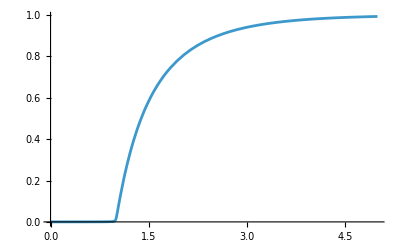

```mathematica
(*Plot[f[x], {x, xmin, xmax},
  PlotRange -> All,
  AxesLabel -> {"x", "f(x)"},
  PlotStyle -> Thick
]
*)
Plot[modSIRend[10^-4, 1/7, R0, 10000/R0],{R0,0,5}]
```

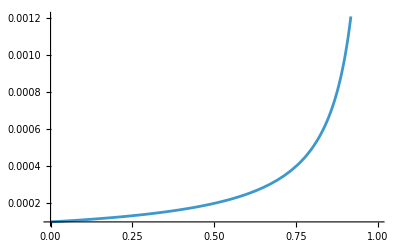

```mathematica
Plot[modSIRend[10^-4, 1/7, R0, 10000/R0],{R0, 0, 0.999}]
```

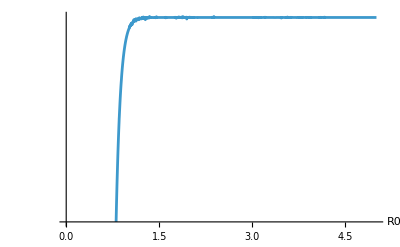

```mathematica
LogPlot[modSIRend[10^-4, 1/7. R0, 10000/R0],{R0,0,5},AxesLabel->Automatic, PlotLegends ->"r(tend)"]
```

### 2 Element Windkessel Model

```mathematica
Remove["Global`*"]
```

```mathematica
(*The Windkessel model is like the low pass filter but in here the resistance and the capacitance are in parallel
Writing down the Kirchoff's equation*)
eqs = {Q == QR+QC, QR*R ==P, QC ==Ca*dP}
```

{Q==QC+QR,QR R==P,QC==Ca dP}

```mathematica
(*We now need to isolate the dP term hence we use this but this doesnot work*)
rule1p = Solve [eqs, {dP}]//Flatten
```

{}

```mathematica
(*we must eliminate all the flows except for Q*)
Eliminate[eqs, {QR,QC}]
```

P+Ca dP R-Q R==0

```mathematica
rule1 = Solve[eqs, {dP}, {QR, QC}]//Flatten
```

{dP→-(P-Q R)/(Ca R)}

```mathematica
ode = D[P[t], t]==dP /.rule1
```

P'[t]==-(P-Q R)/(Ca R)

```mathematica
(*We have a variable Q so we need to define the Inflow function
   - Period = 1
   - Nonzero only in the first 0.4 units of each cycle
   - Shape: smooth cosine bump from 0 up to I0 and back to 0
   - Otherwise = 0*)
Inflow[t_, I0_] := 
  Piecewise[{{I0 (1 - Cos[2 Pi*Mod[t, 1]/0.4])/2, Mod[t, 1] < 0.4}}, 0]
```

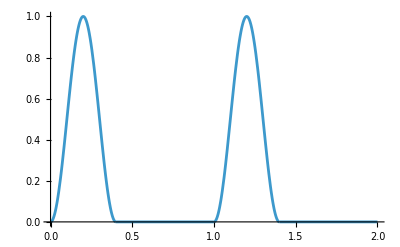

```mathematica
Plot[Inflow[t,1],{t,0,2}]
```

```mathematica
(* Rearrange the ODE and apply initial conditions
*)
ode2W = {P'[t]*Ca+P[t]/R==Inflow[t, I0],P[0]==0}
```

{P[t]/R+Ca P'[t]==(Piecewise[{{1/2 I0 (1-Cos[15.708 Mod[t,1]]), Mod[t,1]<0.4}, {0, True}}]),P[0]==0}

```mathematica
values = {I0->1, R->1, Ca->1}
(* Numerically Solve this ODE using NDSolveValue
*)
P2Wt = NDSolveValue[ode2W/. values, P, {t,0,4}]
Print["Original ode2W:"]
Print[ode2W]
ode2WSub=ode2W/. values;
Print["After substituting numeric values:"]
Print[ode2WSub]
```

{I0→1,R→1,Ca→1}

InterpolatingFunction[…]

Original ode2W:

{P[t]/R+Ca P'[t]==(Piecewise[{{1/2 I0 (1-Cos[15.708 Mod[t,1]]), Mod[t,1]<0.4}, {0, True}}]),P[0]==0}

After substituting numeric values:

{P[t]+P'[t]==(Piecewise[{{1/2 (1-Cos[15.708 Mod[t,1]]), Mod[t,1]<0.4}, {0, True}}]),P[0]==0}

```mathematica
P2Wt[1]
```

0.0901009

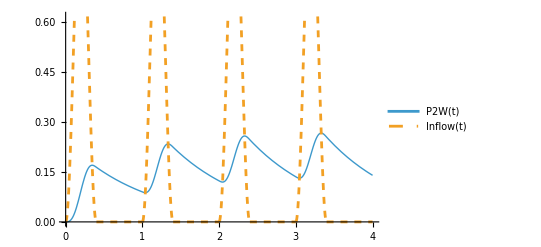

```mathematica
Plot[
 {P2Wt[t], Inflow[t, 1]}, 
 {t, 0, 4}, 
 PlotLegends -> {"P2W(t)", "Inflow(t)"}, 
 PlotStyle -> {Thick, Dashed}
]
```

```mathematica
Windkessel2element[I0_: 1, R_: 1, Ca_: 1, tend_: 4] := 
 Module[{ode2W, P2Wt, Inflow},
  
  (* Define inflow function *)
  Inflow[t_] := 
   Piecewise[{{I0 (1 - Cos[2 Pi*Mod[t, 1]/0.4])/2, Mod[t, 1] < 0.4}}, 0];
  
  (* Define Windkessel ODE *)
  ode2W = {P'[t]*Ca + P[t]/R == Inflow[t], P[0] == 0};
  
  (* Solve ODE numerically *)
  P2Wt = NDSolveValue[ode2W, P, {t, 0, tend}];
  
  (* Plot pressure and inflow *)
  Plot[{P2Wt[t], Inflow[t]}, {t, 0, tend},
   PlotLegends -> {"P₂W(t)", "Inflow(t)"},
   PlotStyle -> {Thick, Dashed},
   AxesLabel -> {"t", "Value"},
   PlotLabel -> "2-Element Windkessel Model"
   ]
  ]
```

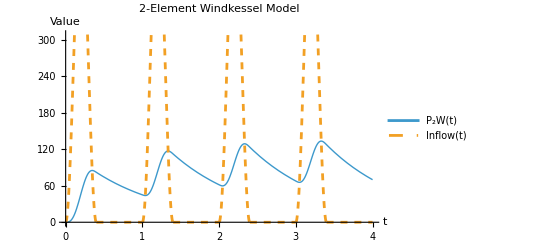

```mathematica
Windkessel2element[500]
```

### 3 Element Windkessel Model

```mathematica
Remove["Global`*"]
```

```mathematica
eqs3 = {Q ==QC+QR, QR*R2+Q*R1 ==P, QC ==Ca*dP2, P2 ==QR*R2,dP==dP2+dQ*R1}
```

{Q==QC+QR,Q R1+QR R2==P,QC==Ca dP2,P2==QR R2,dP==dP2+dQ R1}

```mathematica
eqs4 = Eliminate[eqs3, {QR,QC}]
```

-dQ P+dQ P2+dP Q-dP2 Q==0&&-dP+dP2+dQ R1==0&&-P+P2+Q R1==0&&P2+Ca dP2 R2-Q R2==0

```mathematica
sol3w = Solve[eqs3, dP, {QR, QC, P2, dP2}]//Flatten
```

{dP→-(P-Q R1-Q R2-Ca dQ R1 R2)/(Ca R2)}

```mathematica
ode3W = {(1+R1/R2)Inflow[t]+Ca*R1*dInflow[t]==P[t]/R2+Ca*P'[t],P[0]==0}
```

{Ca R1 dInflow[t]+(1+R1/R2) Inflow[t]==P[t]/R2+Ca P'[t],P[0]==0}

```mathematica
Inflow[t_]:= Piecewise[{{I0(1-Cos[2 Pi*Mod[t,1]/0.4])/2,Mod[t,1]<0.4}}]
dInflow[t_] := Piecewise[{{I0(Sin[2 Pi*Mod[t,1]/0.4])*Pi/0.4,Mod[t,1]<0.4}}]
```

```mathematica
values = {I0->1, R1->1,R2->1, Ca->1}
(* Numerically Solve this ODE using NDSolveValue
*)
P3Wt = NDSolveValue[ode3W/. values, P, {t,0,4}]
Print["Original ode2W:"]
Print[ode3W]
ode3WSub=ode3W/. values;
Print["After substituting numeric values:"]
Print[ode3WSub]
```

{I0→1,R1→1,R2→1,Ca→1}

InterpolatingFunction[…]

Original ode2W:

{(1+R1/R2) (Piecewise[{{1/2 I0 (1-Cos[15.708 Mod[t,1]]), Mod[t,1]<0.4}, {0, True}}])+Ca R1 (Piecewise[{{7.85398 I0 Sin[15.708 Mod[t,1]], Mod[t,1]<0.4}, {0, True}}])==P[t]/R2+Ca P'[t],P[0]==0}

After substituting numeric values:

{2 (Piecewise[{{1/2 (1-Cos[15.708 Mod[t,1]]), Mod[t,1]<0.4}, {0, True}}])+(Piecewise[{{7.85398 Sin[15.708 Mod[t,1]], Mod[t,1]<0.4}, {0, True}}])==P[t]+P'[t],P[0]==0}

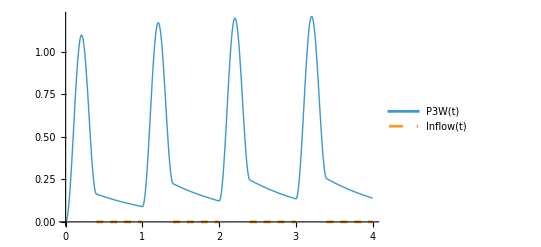

```mathematica
Plot[
 {P3Wt[t], Inflow[t]}, 
 {t, 0, 4}, 
 PlotLegends -> {"P3W(t)", "Inflow(t)"}, 
 PlotStyle -> {Thick, Dashed}
]
```